# Ellipse → Central Force

```mathematica
r={a Cos[θ],b Sin[θ]};
rr= D[r,θ]
rrr=D[rr,θ]
```

{-a Sin[θ],b Cos[θ]}

{-a Cos[θ],-b Sin[θ]}

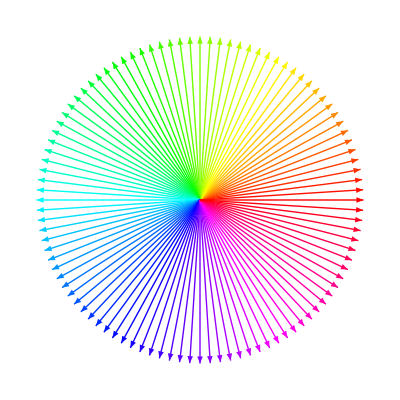

```mathematica
Graphics[Table[{Hue[k/100],Arrow[{{0,0},{Cos[2k Pi/100],Sin[2k Pi /100]}}]},{k,100}]]
```

```mathematica
n=20;
Manipulate[
Show[
Graphics[Table[{Hue[k/n],Arrow[{{a Cos[2k Pi/n],b Sin[2k Pi/n]},{a Cos[2k Pi/n],b Sin[2k Pi/n]}+{-a Sin[2k Pi/n],b Cos[2k Pi/n]}/2}]},{k,n}],Axes->True],
Graphics[Table[{Hue[k/n],Arrow[{{a Cos[2k Pi/n],b Sin[2k Pi/n]},{a Cos[2k Pi/n],b Sin[2k Pi/n]}+{-a Cos[2k Pi/n],-b Sin[2k Pi/n]}/2}]},{k,n}],Axes->True],
ParametricPlot[
{{a Cos[θ],b Sin[θ]}
}
,{θ,0,2π},PlotRange->3]
]
,{{a,2},1,3},{{b,1},1,3}]
```

```mathematica
D[a/(1+c Cos[θ]),θ]
```

(a c Sin[θ])/(1+c Cos[θ])^2

```mathematica
Manipulate[
PolarPlot[{a/(1+c Cos[θ]),(a c Sin[θ])/(1+c Cos[θ])^2},{θ,0,2π-0.5}],
{a,1,3},{c,0,2}]
```

```mathematica
Manipulate[
ParametricPlot[
a/(1-c Cos[θ]){Cos[θ],Sin[θ]}
,{θ,0,2π}],
{a,1,3},{{c,0.5},0,1}]
```

```mathematica
(* The problem is we assumed the particle move uniformly alone the curve *)
```

```mathematica
pr=a/(1+c Cos[θ]){Cos[θ],Sin[θ]}
prr=D[pr,θ]//Simplify
prrr=D[prr,θ]//Simplify
```

{(a Cos[θ])/(1+c Cos[θ]),(a Sin[θ])/(1+c Cos[θ])}

{-(a Sin[θ])/(1+c Cos[θ])^2,(a (c+Cos[θ]))/(1+c Cos[θ])^2}

{-(a (Cos[θ]+c Cos[θ]^2+2 c Sin[θ]^2))/(1+c Cos[θ])^3,(a (-1+2 c^2+c Cos[θ]) Sin[θ])/(1+c Cos[θ])^3}

```mathematica
n=40;
Manipulate[
Show[
Graphics[
Table[
{Hue[k/n],
Arrow[{
{(a Cos[(2k Pi)/n])/(1+c Cos[(2k Pi)/n]),(a Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])},{(a Cos[(2k Pi)/n])/(1+c Cos[(2k Pi)/n]),(a Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])}+{-(a Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])^2,(a (c+Cos[(2k Pi)/n]))/(1+c Cos[(2k Pi)/n])^2}/2
}]
}
,{k,n}]
,Axes->True],
Graphics[Table[{Hue[k/n],Arrow[{
{(a Cos[(2k Pi)/n])/(1+c Cos[(2k Pi)/n]),(a Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])},{(a Cos[(2k Pi)/n])/(1+c Cos[(2k Pi)/n]),(a Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])}+{-(a (Cos[(2k Pi)/n]+c Cos[(2k Pi)/n]^2+2 c Sin[(2k Pi)/n]^2))/(1+c Cos[(2k Pi)/n])^3,(a (-1+2 c^2+c Cos[(2k Pi)/n]) Sin[(2k Pi)/n])/(1+c Cos[(2k Pi)/n])^3}/2
}]},{k,n}],Axes->True],
ParametricPlot[
a/(1+c Cos[θ]){Cos[θ],Sin[θ]}
,{θ,0,2π},PlotRange->3]
]
,{{a,1},1,3},{{c,0.5},0,1}]
```